#1 Perfect plasticity

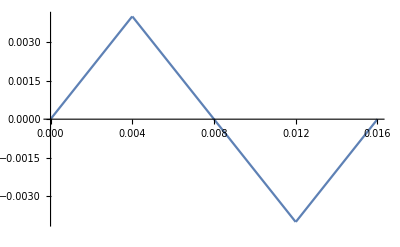

```mathematica
Subscript[σ, Y]=3*10^8;
El = 210*10^9;
ep=Subscript[σ, Y]/El;
e[t_]:=Piecewise[{{t, 0≤ t<0.004}, {0.008-t, 0.004≤ t<0.012}, {t-0.016, 0.012≤t≤ 0.016}}]
Plot[e[t],{t,0,0.016}]
```

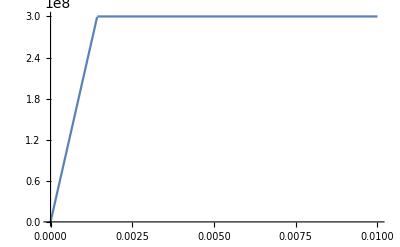

```mathematica
sigma[x_]:=Piecewise[{{El*x, 0<Abs[x]<ep}, {Sign[x] Subscript[σ, Y], Abs[x]>ep}}]
Plot[sigma[x],{x,0,0.01}]
(*ParametricPlot[{e[x],sigma[e[x]]},{x,0,0.016}]*)
```

```mathematica
Table[{e[x],sigma[e[x]]},{x,0,0.016,0.0001}]
```

{{0.,0},{0.0001,2.1×10^7},{0.0002,4.2×10^7},{0.0003,6.3×10^7},{0.0004,8.4×10^7},{0.0005,1.05×10^8},{0.0006,1.26×10^8},{0.0007,1.47×10^8},{0.0008,1.68×10^8},{0.0009,1.89×10^8},{0.001,2.1×10^8},{0.0011,2.31×10^8},{0.0012,2.52×10^8},{0.0013,2.73×10^8},{0.0014,2.94×10^8},{0.0015,300000000},{0.0016,300000000},{0.0017,300000000},{0.0018,300000000},{0.0019,300000000},{0.002,300000000},{0.0021,300000000},{0.0022,300000000},{0.0023,300000000},{0.0024,300000000},{0.0025,300000000},{0.0026,300000000},{0.0027,300000000},{0.0028,300000000},{0.0029,300000000},{0.003,300000000},{0.0031,300000000},{0.0032,300000000},{0.0033,300000000},{0.0034,300000000},{0.0035,300000000},{0.0036,300000000},{0.0037,300000000},{0.0038,300000000},{0.0039,300000000},{0.004,300000000},{0.0039,300000000},{0.0038,300000000},{0.0037,300000000},{0.0036,300000000},{0.0035,300000000},{0.0034,300000000},{0.0033,300000000},{0.0032,300000000},{0.0031,300000000},{0.003,300000000},{0.0029,300000000},{0.0028,300000000},{0.0027,300000000},{0.0026,300000000},{0.0025,300000000},{0.0024,300000000},{0.0023,300000000},{0.0022,300000000},{0.0021,300000000},{0.002,300000000},{0.0019,300000000},{0.0018,300000000},{0.0017,300000000},{0.0016,300000000},{0.0015,300000000},{0.0014,2.94×10^8},{0.0013,2.73×10^8},{0.0012,2.52×10^8},{0.0011,2.31×10^8},{0.001,2.1×10^8},{0.0009,1.89×10^8},{0.0008,1.68×10^8},{0.0007,1.47×10^8},{0.0006,1.26×10^8},{0.0005,1.05×10^8},{0.0004,8.4×10^7},{0.0003,6.3×10^7},{0.0002,4.2×10^7},{0.0001,2.1×10^7},{0.,0},{-0.0001,-2.1×10^7},{-0.0002,-4.2×10^7},{-0.0003,-6.3×10^7},{-0.0004,-8.4×10^7},{-0.0005,-1.05×10^8},{-0.0006,-1.26×10^8},{-0.0007,-1.47×10^8},{-0.0008,-1.68×10^8},{-0.0009,-1.89×10^8},{-0.001,-2.1×10^8},{-0.0011,-2.31×10^8},{-0.0012,-2.52×10^8},{-0.0013,-2.73×10^8},{-0.0014,-2.94×10^8},{-0.0015,-300000000},{-0.0016,-300000000},{-0.0017,-300000000},{-0.0018,-300000000},{-0.0019,-300000000},{-0.002,-300000000},{-0.0021,-300000000},{-0.0022,-300000000},{-0.0023,-300000000},{-0.0024,-300000000},{-0.0025,-300000000},{-0.0026,-300000000},{-0.0027,-300000000},{-0.0028,-300000000},{-0.0029,-300000000},{-0.003,-300000000},{-0.0031,-300000000},{-0.0032,-300000000},{-0.0033,-300000000},{-0.0034,-300000000},{-0.0035,-300000000},{-0.0036,-300000000},{-0.0037,-300000000},{-0.0038,-300000000},{-0.0039,-300000000},{-0.004,-300000000},{-0.0039,-300000000},{-0.0038,-300000000},{-0.0037,-300000000},{-0.0036,-300000000},{-0.0035,-300000000},{-0.0034,-300000000},{-0.0033,-300000000},{-0.0032,-300000000},{-0.0031,-300000000},{-0.003,-300000000},{-0.0029,-300000000},{-0.0028,-300000000},{-0.0027,-300000000},{-0.0026,-300000000},{-0.0025,-300000000},{-0.0024,-300000000},{-0.0023,-300000000},{-0.0022,-300000000},{-0.0021,-300000000},{-0.002,-300000000},{-0.0019,-300000000},{-0.0018,-300000000},{-0.0017,-300000000},{-0.0016,-300000000},{-0.0015,-300000000},{-0.0014,-2.94×10^8},{-0.0013,-2.73×10^8},{-0.0012,-2.52×10^8},{-0.0011,-2.31×10^8},{-0.001,-2.1×10^8},{-0.0009,-1.89×10^8},{-0.0008,-1.68×10^8},{-0.0007,-1.47×10^8},{-0.0006,-1.26×10^8},{-0.0005,-1.05×10^8},{-0.0004,-8.4×10^7},{-0.0003,-6.3×10^7},{-0.0002,-4.2×10^7},{-0.0001,-2.1×10^7},{0.,0}}

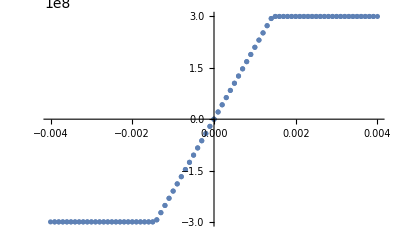

```mathematica
ListPlot[%22]
```

#2 Isotropic hardening (linear)

```mathematica
??Global`*
```

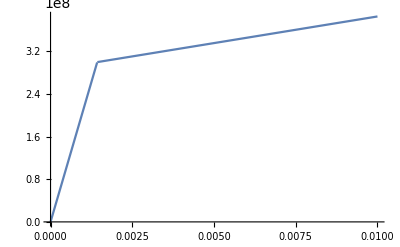

```mathematica
Subscript[σ, Y]=3*10^8;
K=1*10^10;
El = 210*10^9;
ep=Subscript[σ, Y]/El;
Subscript[K, 1][α_]:=Subscript[σ, Y]+K α;
sigma[x_]:=Piecewise[{{El*x, 0<Abs[x]<ep}, {Sign[x]Subscript[K, 1][x-ep], x>ep}}]
Plot[sigma[x],{x,0,0.01},AxesOrigin->{0,0}]
```

```mathematica
Grid[Table[{i,Subscript[K, 1][i]},{i,0,0.02,0.005}]]
```

0. | 3.×10^8
0.005 | 3.5×10^8
0.01 | 4.×10^8
0.015 | 4.5×10^8
0.02 | 5.×10^8

#3 Alternative isotropic hardening (exponential)

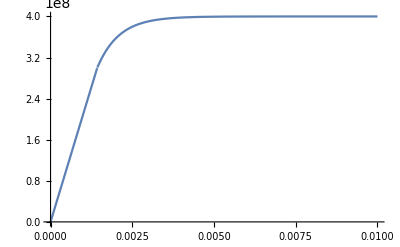

```mathematica
Subscript[σ, Y]=3*10^8;
El = 210*10^9;
ep=Subscript[σ, Y]/El;
K=1*10^8; 
H=0;
θ=1;
δ=1500;
Subscript[K, 2][α_]:=Subscript[σ, Y]+θ H α+K(1-Exp[-δ α]);
sigma[x_]:=Piecewise[{{El*x, 0<x<ep}, {Subscript[K, 2][x-ep], x>ep}}]
Plot[sigma[x],{x,0,0.01},AxesOrigin->{0,0}]
```

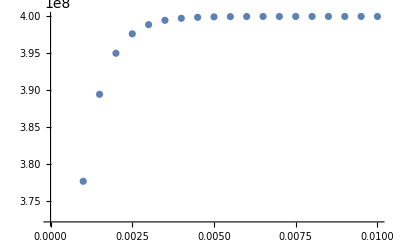

```mathematica
ListPlot[Table[{i,Subscript[K, 2][i]},{i,0,0.01,0.0005}]]
```

```mathematica
Grid[Table[{i,Subscript[K, 2][i]},{i,0,0.01,0.0005}]]
```

0. | 3.×10^8
0.0005 | 3.52763×10^8
0.001 | 3.77687×10^8
0.0015 | 3.8946×10^8
0.002 | 3.95021×10^8
0.0025 | 3.97648×10^8
0.003 | 3.98889×10^8
0.0035 | 3.99475×10^8
0.004 | 3.99752×10^8
0.0045 | 3.99883×10^8
0.005 | 3.99945×10^8
0.0055 | 3.99974×10^8
0.006 | 3.99988×10^8
0.0065 | 3.99994×10^8
0.007 | 3.99997×10^8
0.0075 | 3.99999×10^8
0.008 | 3.99999×10^8
0.0085 | 4.×10^8
0.009 | 4.×10^8
0.0095 | 4.×10^8
0.01 | 4.×10^8

#4 Kinematic hardening

```mathematica
Subscript[σ, Y]=3*10^8;
El = 210*10^9;
ep=Subscript[σ, Y]/El;
K=1*10^8; 
H=0;
θ=1;
dH=(1-θ)H;
δ=1500;
Subscript[K, 3][α_]:=Subscript[σ, Y]+θ H α+K(1-Exp[-δ α]);
sigma[x_]:=Piecewise[{{El*x, 0<x<ep}, {Subscript[K, 3][x-ep], x>ep}}]
Plot[sigma[x],{x,0,0.01},AxesOrigin->{0,0}]
```

-Graphics-